```mathematica
(*Initiation: *)
```

```mathematica
v=9;
ive[v][5]=Interpolation[vel5v9];
ive[v][10]=Interpolation[vel10v9];
ive[v][20]=Interpolation[vel20v9];
ive[v][30]=Interpolation[vel30v9];
ive[v][40]=Interpolation[vel40v9];
ive[v][50]=Interpolation[vel50v9];
```

```mathematica
v=9;
ve[v][5]= vel5v9;
ve[v][10]= vel10v9;
ve[v][20]= vel20v9;
ve[v][30]= vel30v9;
ve[v][40]= vel40v9;
ve[v][50]= vel50v9;
```

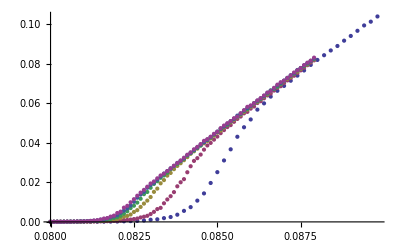

```mathematica
ListPlot[{vel5v9,vel10v9,vel20v9,vel30v9,vel40v9,vel50v9}]
```

```mathematica
δ=0.0008;
v=9;
Do[
dvedd[v][l]=Table[{x,(ive[v][l][x+δ]-ive[v][l][x-δ])/(2*δ)},{x,0.0815,0.087,0.0002}];
,{l,{5,10,20,30,40,50}}]
```

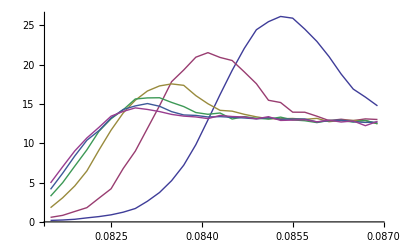

```mathematica
ListLinePlot[{dvedd[v][5],dvedd[v][10],dvedd[v][20],dvedd[v][30],dvedd[v][40],dvedd[v][50]}]
```

```mathematica
maxdvedd[v]=Table[{l*1000,Max[dvedd[v][l][[All,2]]]},{l,{5,10,20,30,40,50}}]
Logmaxdvedd[v]=Table[{Log[maxdvedd[v][[All,1]][[i]]],Log[maxdvedd[v][[All,2]][[i]]]},{i,1,Length[maxdvedd[v]]}]

pmaxdvedd[v]=Table[{maxdvedd[v][[All,1]][[i]],Select[dvedd[v][maxdvedd[v][[All,1]][[i]]/1000],#[[2]]==maxdvedd[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdvedd[v]]}]


vvpmaxdvedd[v]=Table[{pmaxdvedd[v][[All,1]][[i]],Select[ve[v][pmaxdvedd[v][[All,1]][[i]]/1000],#[[1]]==pmaxdvedd[v][[All,2]][[i]]&][[All,2]][[1]]},{i,1,Length[pmaxdvedd[v]]}]

vvpmaxdvedd[v]={{5000,0.033825213125},{10000,0.02507711},{20000,0.02338075},{30000,0.022270459999999995},{40000,0.019740129999999998},{50000,0.017782430000000002}}



Logvvpmaxdvedd[v]=Table[{Log[vvpmaxdvedd[v][[All,1]][[i]]],Log[vvpmaxdvedd[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdvedd[v]]}]
```

{{5000,26.1494},{10000,21.5425},{20000,17.5633},{30000,15.8033},{40000,15.0635},{50000,14.5124}}

{{Log[5000],3.26383},{Log[10000],3.07003},{Log[20000],2.86581},{Log[30000],2.76022},{Log[40000],2.71228},{Log[50000],2.675}}

{{5000,0.0853},{10000,0.0841},{20000,0.0835},{30000,0.0833},{40000,0.0831},{50000,0.0829}}

{{5000,{}⟦1⟧},{10000,0.0250771},{20000,0.0233808},{30000,0.0222705},{40000,0.0197401},{50000,0.0177824}}

{{5000,0.0338252},{10000,0.0250771},{20000,0.0233808},{30000,0.0222705},{40000,0.0197401},{50000,0.0177824}}

{{Log[5000],-3.38655},{Log[10000],-3.6858},{Log[20000],-3.75584},{Log[30000],-3.80449},{Log[40000],-3.9251},{Log[50000],-4.02954}}

```mathematica
ive[9][5][0.0853]
```

0.0338252

```mathematica
------------------------------------------------------------------------------------------
```

```mathematica
v=9;
Logmaxdvedd[v]
Logvvpmaxdvedd[v]
pmaxdvedd[v]
```

{{Log[5000],3.26383},{Log[10000],3.07003},{Log[20000],2.86581},{Log[30000],2.76022},{Log[50000],2.675}}

{{Log[5000],-3.38655},{Log[10000],-3.6858},{Log[20000],-3.75584},{Log[30000],-3.80449},{Log[50000],-4.02954}}

{{5000,0.0853},{10000,0.0841},{20000,0.0835},{30000,0.0833},{50000,0.0829}}

```mathematica
Logmaxdvedd[v]={{Log[5000],3.2638262755734315},{Log[10000],3.070027060845957},{Log[20000],2.865812849908593},{Log[30000],2.7602185812405144},{Log[50000],2.6750047053198958}};
```

```mathematica
Logvvpmaxdvedd[v]={{Log[5000],-3.386548804132127},{Log[10000],-3.685799801117017},{Log[20000],-3.755842244752982},{Log[30000],-3.804494142335704},{Log[50000],-4.029544387818731}};
```

```mathematica
pmaxdvedd[v]={{5000,0.0853},{10000,0.08410000000000001},{20000,0.0835},{30000,0.0833},{50000,0.0829}};
```

```mathematica
ν=1/0.09;
k0=0.08122;
ClearAll[a0,b0,d0,ex0,c0]
model1=a0*x-b0;
model2=d0+c0*x^(-ex0)
model3=d0+c0*x^(-1/ν)
model4=k0+c0*x^(-ex0)

nlf1=NonlinearModelFit[Logvvpmaxdvedd[v],model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxdvedd[v],model2,{d0,c0,ex0},x];

nlf2[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[pmaxdvedd[v],model3,{d0,c0},x];

nlf3[{"BestFit","ParameterTable"}]


nlf4=NonlinearModelFit[pmaxdvedd[v],model4,{ex0,c0},x];

nlf4[{"BestFit","ParameterTable"}]
```

d0+c0 x^-ex0

d0+c0/x^0.09

0.08122+c0 x^-ex0

{-1.32281-0.247092 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -1.32281 | 0.37973 | -3.48356 | 0.0399522
b0 | 0.247092 | 0.0388048 | 6.36758 | 0.00783921}

{0.08382-442.003/x^58.4948, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.08382 | 0.000590593 | 141.925 | 0.0000496419
c0 | -442.003 | 0. | -∞ | 0.
ex0 | 58.4948 | 0. | ∞ | 0.}

{0.0727055+0.0266623/x^0.09, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.0727055 | 0.00131749 | 55.1846 | 0.000013107
c0 | 0.0266623 | 0.00315196 | 8.45895 | 0.0034681}

{0.08122+0.10913/x^0.388496, | Estimate | Standard Error | t-Statistic | P-Value
ex0 | 0.388496 | 0.0274275 | 14.1645 | 0.000762307
c0 | 0.10913 | 0.0277715 | 3.92957 | 0.0293385}

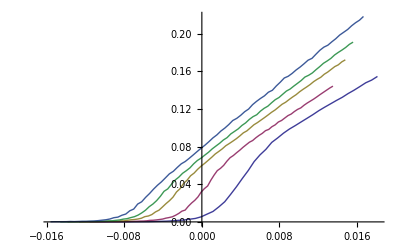

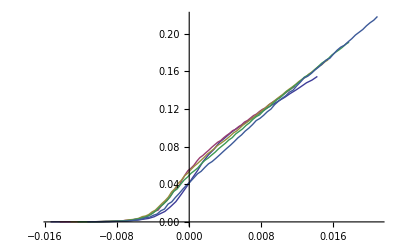

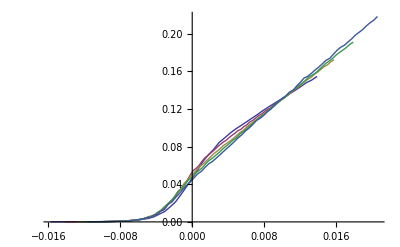

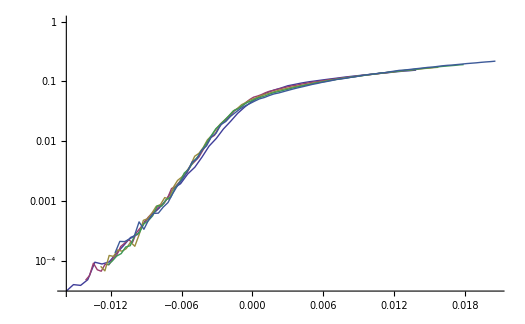

```mathematica
b0=0.13;
k01=nlf2["ParameterTableEntries"][[1]][[1]];
k02=nlf3["ParameterTableEntries"][[1]][[1]];
k03=k0;
ex01=-nlf2["ParameterTableEntries"][[3]][[1]];
ex02=-1/ν;
ex03=-nlf4["ParameterTableEntries"][[1]][[1]];
a=-nlf1["ParameterTableEntries"][[2]][[1]];
c01=nlf2["ParameterTableEntries"][[2]][[1]];
c02=nlf3["ParameterTableEntries"][[2]][[1]];
c03=nlf4["ParameterTableEntries"][[2]][[1]];


Do[

(*absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

ves1[v][l]=Table[{(ve[v][l][[All,1]][[i]]-(k01+c01*(l*1000)^(ex01)))*(l*1000)^b0,ve[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[ve[v][l]]}];

ves2[v][l]=Table[{(ve[v][l][[All,1]][[i]]-(k02+c02*(l*1000)^(ex02)))*(l*1000)^b0,ve[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[ve[v][l]]}];

ves3[v][l]=Table[{(ve[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03)))*(l*1000)^b0,ve[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[ve[v][l]]}];

,{l,{5,10,20,30,50}}]
(*ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]*)
ListPlot[{ves1[v][5],ves1[v][10],ves1[v][20],ves1[v][30],ves1[v][50]},Joined->True]
ListPlot[{ves2[v][5],ves2[v][10],ves2[v][20],ves2[v][30],ves2[v][50]},Joined->True]
ListPlot[{ves3[v][5],ves3[v][10],ves3[v][20],ves3[v][30],ves3[v][50]},Joined->True]
ListLogPlot[{ves3[v][5],ves3[v][10],ves3[v][20],ves3[v][30],ves3[v][50]},Joined->True]
```

```mathematica
l1=10;
l2=50;

Do[
(*input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

input3[l]=Table[{(ve[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03))),ve[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[ve[v][l]]}];
,{l,{l1,l2}}]

aux=1000;
For[z=-0.2,z<0.4,z+=0.01,
ClearAll[i];

Do[
dat[l]=Table[{input3[l][[All,1]][[i]]*(l*1000)^z,input3[l][[All,2]][[i]]},{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]]];

val=NIntegrate[Abs[i[l1][x]-i[l2][x]],{x,min,max}]/(max-min);
(*Print[val]*)

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

0.0032912

0.13 = zf

```mathematica
l1=5;
l2=20;
l3=30;
l4=50;
sum={};

Do[
(*input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

input3[l]=Table[{(ve[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03))),ve[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[ve[v][l]]}];
,{l,{l1,l2,l3,l4}}]

aux=1000;
For[z=-0.4,z<0.4,z+=0.01,
ClearAll[i];

Do[
dat[l]=Table[{input3[l][[All,1]][[i]]*(l*1000)^z,input3[l][[All,2]][[i]]},{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Max[i[l1][x],i[l2][x],i[l3][x],i[l4][x]]-Min[i[l1][x],i[l2][x],i[l3][x],i[l4][x]]],{x,min,max}]/(max-min);
(*Print[val]*)
sum=Append[sum,{z,val}];

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

0.00496301

0.13 = zf

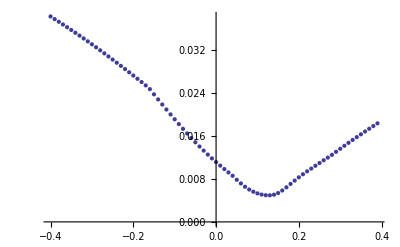

```mathematica
ListPlot[sum]
```